## Larvae burden in diaphragm

### Data

```mathematica
dir = NotebookDirectory[]
```

/Volumes/data4/Projecten/V092112 Trichinella/AAA/Model/Swine infection/

```mathematica
FileNames["Polish*",dir]
```

{}

```mathematica
infile = "R:\\Z&O\\Projecten\\Dier en Vector\\Parasitologie\\Trichinella QMRA\\Polish samples with LPG-abstract.xlsx"
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Polish samples with LPG-abstract.xlsx

Network path is little different on my machine.

```mathematica
infile = "/Volumes/data4/Z&O/Projecten/Dier en Vector/Parasitologie/Trichinella QMRA/Polish samples with LPG-abstract.xlsx"
```

/Volumes/data4/Z&O/Projecten/Dier en Vector/Parasitologie/Trichinella QMRA/Polish samples with LPG-abstract.xlsx

```mathematica
df = Import[infile];
```

```mathematica
df= df[[1]];
```

```mathematica
lpg = df[[2;;,7]]
```

{7.6,4.02,0.3,42.8,33.1,12.,13.,0.3,41.,1.9,4.,10.,2.4,1.4,6.,63.,4.92,0.22,89.,19.52,47.,2.4,3.,4.1,69.,4.92,56.,211.,0.8,0.9,94.,0.56,2.12,1.5}

```mathematica
lpg = IntegerPart[50 lpg]
```

{380,200,15,2140,1655,600,650,15,2050,95,200,500,120,70,300,3150,246,11,4450,976,2350,120,150,204,3450,246,2800,10550,40,45,4700,28,106,75}

This is perhaps more consistent data specification.

```mathematica
{examined,positive}={24*10^8,1}+{Length@lpg, Length@lpg}
```

{2400000034,35}

```mathematica
Total[ lpg ] / examined // N
```

0.0000177862

### Estimation

```mathematica
f=Binomial[x+k-1,k-1] (m/k)^x(1+m/k)^(-k-x)
```

(m/k)^x (1+m/k)^(-k-x) Binomial[-1+k+x,-1+k]

```mathematica
g = N@LogLikelihood[BinomialDistribution[examined,1-f/.x-> 0],{positive}]
```

663.82+2.4×10^9 Log[(1.+m/k)^(-1. k)]+35. Log[1.-1. (1.+m/k)^(-1. k)]

```mathematica
lik=.
```

```mathematica
lik:=∏_(i=1)^n (f/.{x->Subscript[x, i]})
```

```mathematica
lik
```

∏_(i=1)^n (m/k)^x_i (1+m/k)^(-k-x_i) Binomial[-1+k+x_i,-1+k]

```mathematica
Remove@obslik
obslik:=g +Log[lik]/.{n:>Length[lpg],Subscript[x, i_]:>lpg[[i]]}
```

```mathematica
sol = NMaximize[{obslik,0<m ,0<k },{m,k}, MaxIterations->300]
```

{-879.333,{m→0.000036096,k→3.06724×10^-9}}

```mathematica
N[positive/examined]
```

1.45833×10^-8

It is not exactly the same but a lot closer than it was.

```mathematica
N[1-Table[f/.sol[[2]],{x,0,3}], 5]
```

{2.875×10^-8,1.,1.,1.}

```mathematica
1-(1+m/k)^(-k) /. sol[[2]]
```

2.875×10^-8

## Larvae recovery

### Data

```mathematica
dir = NotebookDirectory[]
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\

```mathematica
FileNames["Larva*.xlsx",dir]
```

{R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Larval recovery NL trich labs.xlsx}

```mathematica
infile="R:\\Z&O\\Projecten\\Dier en Vector\\Parasitologie\\Trichinella QMRA\\Larval recovery NL trich labs.xlsx"
```

R:\Z&O\Projecten\Dier en Vector\Parasitologie\Trichinella QMRA\Larval recovery NL trich labs.xlsx

```mathematica
data=Import[infile]//First;
```

Exclude zero spike.

```mathematica
data=Cases[data,{x_,y_}/;0<x<1000];
```

{{5.,5.},{5.,5.},{7.,7.},{9.,4.},{5.,5.},{5.,4.},{7.,7.},{9.,4.},{5.,5.},{5.,4.},{7.,7.},{9.,6.},{5.,4.},{5.,4.},{7.,7.},{9.,4.},{9.,8.},{5.,5.},{5.,5.},{7.,6.},{9.,7.},{5.,6.},{5.,4.},{7.,7.},{9.,8.},{5.,5.},{5.,4.},{7.,6.},{5.,4.},{5.,3.},{7.,5.},{9.,9.},{5.,4.},{5.,3.},{7.,6.},{9.,9.},{5.,4.},{5.,3.},{7.,4.},{9.,8.},{7.,5.},{9.,8.},{5.,4.},{5.,3.},{7.,5.},{9.,6.},{5.,4.},{5.,4.},{7.,4.},{9.,8.},{5.,3.},{5.,2.},{3.,3.},{3.,2.},{8.,7.},{8.,6.},{3.,3.},{3.,3.},{8.,7.},{8.,6.},{3.,3.},{3.,2.},{8.,7.},{8.,6.},{3.,3.},{3.,3.},{8.,7.},{8.,6.},{3.,4.},{3.,3.},{8.,7.},{8.,8.},{3.,3.},{3.,3.},{8.,7.},{8.,7.},{3.,3.},{3.,3.},{8.,7.},{8.,8.},{3.,3.},{3.,2.},{8.,6.},{8.,5.},{3.,2.},{3.,2.},{8.,6.},{8.,5.},{3.,3.},{3.,2.},{8.,7.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,5.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{3.,3.},{3.,1.},{8.,3.},{8.,6.},{5.,5.},{5.,4.},{9.,6.},{9.,7.},{5.,4.},{5.,3.},{9.,8.},{9.,7.},{5.,5.},{5.,3.},{9.,6.},{9.,7.},{5.,5.},{5.,4.},{9.,6.},{9.,6.},{9.,7.},{5.,4.},{9.,9.},{5.,4.},{9.,6.},{5.,5.},{9.,8.},{5.,6.},{9.,7.},{5.,4.},{9.,9.},{5.,4.},{5.,5.},{9.,8.},{5.,3.},{9.,8.},{5.,6.},{9.,8.},{5.,3.},{9.,8.},{5.,5.},{9.,7.},{5.,3.},{9.,8.},{5.,5.},{9.,10.},{5.,3.},{9.,8.},{4.,4.},{8.,6.},{6.,6.},{8.,8.},{4.,5.},{8.,8.},{6.,6.},{8.,8.},{4.,2.},{8.,5.},{6.,6.},{8.,7.},{4.,3.},{8.,6.},{6.,6.},{8.,8.},{4.,4.},{8.,6.},{6.,6.},{8.,8.},{8.,7.},{4.,3.},{8.,8.},{6.,6.},{8.,5.},{4.,4.},{8.,8.},{6.,6.},{8.,5.},{4.,4.},{8.,7.},{6.,6.},{8.,6.},{4.,4.},{8.,7.},{6.,5.},{6.,6.},{8.,8.},{8.,8.},{4.,4.},{6.,5.},{8.,6.},{8.,7.},{4.,4.},{6.,4.},{8.,6.},{8.,6.},{4.,4.},{8.,6.},{4.,4.},{6.,5.},{8.,4.},{8.,5.},{4.,3.},{6.,3.},{8.,6.},{8.,6.},{4.,2.},{6.,3.},{8.,5.},{8.,7.},{4.,3.},{6.,4.},{8.,3.}}

```mathematica
{spike,recovered}=dataᵀ;
```

### Beta binomial model of a single larvae recovery

Parameters α and β are correlated. These transformations makes it easy to maximize the likelihood.

```mathematica
Solve[{α/(α+β)==u,Log[α+β]== v},{α,β}]
```

{{α→ConditionalExpression[ⅇ^v u,-π<Im[v]≤π],β→ConditionalExpression[ⅇ^v-ⅇ^v u,-π<Im[v]≤π]}}

Derive Beta Binomial distribution.

```mathematica
p=.
```

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
PDF[BetaDistribution[a,b],p]
```

Piecewise[{{((1-p)^(-1+b) p^(-1+a))/Beta[a,b], 0<p<1}, {0, True}}]

Parameter mixture.

```mathematica
Integrate[(1-p)^(n-x) p^x Binomial[n,x] ((1-p)^(-1+b) p^(-1+a))/Beta[a,b],{p,0,1}]
```

ConditionalExpression[(Binomial[n,x] Gamma[b+n-x] Gamma[a+x])/(Beta[a,b] Gamma[a+b+n]),Re[a+x]>0&&Re[b+n-x]>0]

Apply the transformaion. Binomial term is constant for all parameter values. Drop it.

```mathematica
(Gamma[b+n-x] Gamma[a+x])/(Beta[a,b] Gamma[a+b+n])/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}
```

(Gamma[n+ⅇ^v (1-u)-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,ⅇ^v (1-u)] Gamma[n+ⅇ^v (1-u)+ⅇ^v u])

Now sinplify.

```mathematica
FullSimplify@((Gamma[n+ⅇ^v (1-u)-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,ⅇ^v (1-u)] Gamma[n+ⅇ^v (1-u)+ⅇ^v u]))
```

(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])

Final difinition.

```mathematica
f=(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])
```

(Gamma[ⅇ^v+n-ⅇ^v u-x] Gamma[ⅇ^v u+x])/(Beta[ⅇ^v u,-ⅇ^v (-1+u)] Gamma[ⅇ^v+n])

Define likelihood.

```mathematica
lik:=∏_(i=1)^s (f/.{n->Subscript[n, i],x->Subscript[x, i]})
```

Insert the data points.

```mathematica
obsloglik:=Log@lik/.{s:> Length[diaphragm],Subscript[n, i]:>spike[[i]],Subscript[x, i]:>recovered[[i]] }
```

Find the maximum likelihood estimates.

When I called the build in Beta binomial distribution, I found that the maximization fails due to memory bust.

Remember:
(1) Define function by your self.
(2) Define function using reals not integers.

```mathematica
nul = NMaximize[{obsloglik,0<u<1},{u,v}]
```

Estimated mean and variance.

```mathematica
{u,(u(1-u))/(1+ⅇ^v)}/.nul[[2]]
```

{0.841435,0.0472264}

Back transform the parameters.

```mathematica
{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

{a→1.53575,b→0.289405}

```mathematica
beta = BetaDistribution[a,b]/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

BetaDistribution[1.53575,0.289405]

Estimated beta distribution.

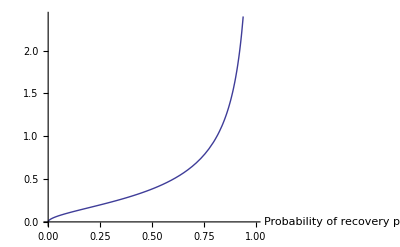

```mathematica
Plot[PDF[beta,x],{x,0,1},AxesLabel->{"Probability of recovery per larva",None}]
```

```mathematica
PDF[BetaBinomialDistribution[a,b,n],0]/.{a-> u ⅇ^v,b->(1-u)ⅇ^v}/.nul[[2]]
```

Piecewise[{{Pochhammer[0.289405,n]/Pochhammer[1.82516,n], 0≤n}, {0, True}}]

```mathematica
recoveryProbability = Table[1-Pochhammer[0.2894050520857973,n]/Pochhammer[1.8251553490608916,n],{n,1,10}];
```

```mathematica
TableForm[recoveryProbability,TableHeadings->Automatic]
```

1 | 0.841435
2 | 0.927631
3 | 0.956686
4 | 0.970472
5 | 0.978257
6 | 0.983149
7 | 0.986456
8 | 0.988813
9 | 0.990562
10 | 0.991901

```mathematica
PDF[BetaBinomialDistribution[a,b,n],x]
```

Piecewise[{{(Binomial[n,x] Pochhammer[a,x] Pochhammer[b,n-x])/Pochhammer[a+b,n], 0≤x≤n}, {0, True}}]

```mathematica
FunctionExpand@PDF[BetaBinomialDistribution[a,b,n],x]
```

Piecewise[{{(Gamma[a+b] Gamma[1+n] Gamma[b+n-x] Gamma[a+x])/(Gamma[a] Gamma[b] Gamma[a+b+n] Gamma[1+n-x] Gamma[1+x]), 0≤x≤n}, {0, True}}]

```mathematica
Simplify@FunctionExpand@PDF[BetaBinomialDistribution[a,b,n],0]
```

Piecewise[{{(Gamma[a+b] Gamma[b+n])/(Gamma[b] Gamma[a+b+n]), 0≤n}, {0, True}}]

```mathematica
FunctionExpand[Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]]
```

(Gamma[a+b] Gamma[1+n] Gamma[b+n-x] Gamma[a+x])/(Gamma[a] Gamma[b] Gamma[a+b+n] Gamma[1+n-x] Gamma[1+x])

```mathematica
FullSimplify[Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]-(Binomial[n,x] Pochhammer[a,x] Pochhammer[b,n-x])/Pochhammer[a+b,n]]
```

0

```mathematica
Binomial[n,x] Beta[x+a,n-x+b]/Beta[a,b]/.x->0
```

Beta[a,b+n]/Beta[a,b]

## Parasite numbers in 5 gram diaphragm

### Question A

From 50 gram if diapfragm only 5 gram (10%) is tested . What is the number of trichinella in 5 gram diaphragm? If the parasite number in 50 gram is negative binomial, is it also negative binomial in which the mean is scaled by 10%?

#### Answer: Negative binomial distribution where the mean is scaled by 10%.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
𝒟=ParameterMixtureDistribution[BinomialDistribution[n,p],n\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]]
```

ParameterMixtureDistribution[BinomialDistribution[n,p],n\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]]

This is the charateristic function.

```mathematica
cf1=CharacteristicFunction[𝒟,t]
```

k^k (k-(-1+ⅇ^(ⅈ t)) m p)^-k

Characteristic function of negative binomial distribution in which the mean is scaled by p.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[k,k/(k+p m)],t]
```

(k/(k+m p-ⅇ^(ⅈ t) m p))^k

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

### Question B:

The number of trichinella in 50 gram of diaphragm is negative binomial distribution. What is the number in 100 gram?

#### Answer: negative binomial distribution where both parameters are scaled by 2.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
𝒟=TransformedDistribution[x+y,{x\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],y\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]} ]
```

NegativeBinomialDistribution[2 k,k/(k+m)]

This is the charateristic function.

```mathematica
cf1=Simplify@CharacteristicFunction[𝒟,t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(2 k)

Characteristic function of negative binomial distribution where both parameters are scaled by 2.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[2 k,(2 k)/(2 k+2 m)],t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(2 k)

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

### Question C:

The number of trichinella in 5 gram of diaphragm is negative binomial distribution. What is the number in 50 gram?

#### Answer: negative binomial distribution where both parameters are scaled by 10.

This is a binomial distribution when the the parameter n is negative binomial distribution.

```mathematica
vars = Array[Subscript[x, #]&,10]
```

{x_1,x_2,x_3,x_4,x_5,x_6,x_7,x_8,x_9,x_10}

```mathematica
dists=Thread[Distributed[vars,ConstantArray[ NegativeBinomialDistribution[k,k/(k+m)],10]]]
```

{x_1\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_2\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_3\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_4\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_5\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_6\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_7\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_8\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_9\[Distributed]NegativeBinomialDistribution[k,k/(k+m)],x_10\[Distributed]NegativeBinomialDistribution[k,k/(k+m)]}

```mathematica
𝒟=TransformedDistribution[Total@vars,dists ]
```

NegativeBinomialDistribution[10 k,k/(k+m)]

This is the charateristic function.

```mathematica
cf1=Simplify@CharacteristicFunction[𝒟,t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(10 k)

Characteristic function of negative binomial distribution where both parameters are scaled by 2.

```mathematica
cf2=Simplify@CharacteristicFunction[NegativeBinomialDistribution[10 k,(10 k)/(10 k+10 m)],t]
```

(k/(k+m-ⅇ^(ⅈ t) m))^(10 k)

The two characteristics functions are equal. Hence, the mixture distribution is negative binomial distribution.

```mathematica
PowerExpand[cf2- ExpandAll@cf1 ]
```

0

## Safety test simulation

In Netherlands, 12 to 15  million domestic pigs slaghtered per year, 3000 wild boar slaughtered per year.

```mathematica
numberOfAnimals = 600000
```

600000

```mathematica
maxrange=20000
```

20000

```mathematica
proportionDiaphragm =N[ 5/100]
```

0.05

```mathematica
𝒩=NegativeBinomialDistribution[2 k,(2 k)/(2 k+2 m)]/.{m->5.244308845834319,k->0.00044705143472671417}
```

NegativeBinomialDistribution[0.000894103,0.0000852378]

```mathematica
p=Table[PDF[𝒩,x],{x,0,maxrange}];
```

```mathematica
𝒟=EmpiricalDistribution[p-> Range[0,maxrange]];
```

```mathematica
p=.
```

```mathematica
animal = RandomVariate[𝒟,numberOfAnimals];
```

```mathematica
infected = Position[animal,x_/;x>0];
```

```mathematica
diaphragm = MapAt[RandomVariate[BinomialDistribution[#,proportionDiaphragm]]&, animal,infected];
```

```mathematica
diaphragmBatch=Partition[diaphragm,20];
```

```mathematica
batchID=Flatten@Array[ConstantArray[#,20]&,Length@diaphragmBatch];
```

```mathematica
batchSum = Total/@diaphragmBatch;
```

```mathematica
recoveryProbability = Map[1-Pochhammer[0.2894050520857973,#]/Pochhammer[1.8251553490608916,#]&,batchSum];
```

```mathematica
outcome = Map[RandomReal[]<#&,recoveryProbability];
```

```mathematica
TableForm[SortBy[ {outcome,batchSum,recoveryProbability}ᵀ ,First ],TableHeadings->{Automatic,{"contaminated", "larvae","recovery prob"}}];
```

```mathematica
Tally@outcome
```

{{False,26896},{True,3104}}

```mathematica
escapedBatchID = Cases[{Union@batchID,batchSum,outcome}ᵀ,{w_,x_,y_}/;x>0&&y==False:> w]
```

{149,280,540,1065,1168,1221,2433,3217,3246,3528,3910,3932,3954,4049,4355,5654,5940,6117,6172,6435,7031,7092,7845,7996,9081,9243,9362,9408,9551,10247,10275,10453,10495,10553,10683,10729,10738,11311,11410,12068,12478,12862,13520,14194,14352,14456,14503,15141,15281,15301,15465,15492,15751,15883,16126,16338,16450,16495,16934,17434,17472,17581,17654,18271,18457,18652,18871,19070,19240,19310,19624,19678,20014,20454,20600,21050,21271,21342,21403,21951,22008,22678,22916,22966,23510,23802,23966,24023,24027,24234,24434,24521,24983,25229,25462,26686,26726,28112,28581,28621,28637,28679,28687,28689,28919,28999,29631}

```mathematica
escapedAnimalID= Position[ batchID,x_/;MemberQ[escapedBatchID,x] ];
```

```mathematica
larvaeEscapedAnimal = Extract[animal,escapedAnimalID];
```

```mathematica
TableForm@Sort@Tally@larvaeEscapedAnimal
```

0 | 2027
1 | 5
2 | 2
3 | 1
4 | 4
5 | 5
6 | 6
7 | 4
8 | 3
9 | 4
10 | 4
11 | 3
12 | 2
13 | 2
14 | 5
15 | 2
17 | 4
18 | 3
19 | 3
21 | 3
22 | 2
25 | 1
26 | 1
29 | 1
30 | 3
31 | 2
32 | 1
33 | 2
34 | 1
35 | 1
39 | 2
41 | 1
42 | 2
43 | 1
44 | 1
46 | 2
47 | 1
51 | 1
53 | 2
54 | 1
55 | 1
56 | 1
58 | 1
63 | 2
70 | 1
75 | 1
77 | 1
81 | 1
84 | 1
85 | 2
95 | 1
106 | 1
128 | 1
129 | 1
132 | 1
253 | 1
411 | 1